```mathematica
NotebookDirectory[]
```

/Users/yqli/Desktop/inf552/

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yqli/Desktop/inf552

```mathematica
data = SemanticImport["/Users/yqli/Desktop/inf552/a1_raw.csv"]
```

Dataset[<>]

```mathematica
test = SemanticImport["/Users/yqli/Desktop/inf552/a2_raw.csv"]
```

Dataset[<>]

```mathematica
c = Classify[data -> "Phase", Method-> "SupportVectorMachine"]
```

ClassifierFunction[…]

```mathematica
testModel = Table[Table[test[[n,x]], {x, 18}] -> test[[n,19]], {n, 1, Length[test]}]
```

{{4.49608,5.58357,1.68939,6.93239,5.43292,1.65058,5.53213,1.4734,1.78244,5.57917,4.10922,1.77759,4.50342,5.20035,1.70377,6.61575,5.20614,1.65457}→E,1262,{3.81556,5.27971,1.63865,6.69994,5.18475,1.51443,5.48009,1.41095,1.69415,5.34333,4.15154,1.69874,4.16996,5.11435,1.62241,6.61583,4.94208,1.54355}→G}
 |  |  |  |

```mathematica
cm = ClassifierMeasurements[c, testModel]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Properties"]
```

{Accuracy,AccuracyRejectionPlot,AreaUnderROCCurve,BestClassifiedExamples,ClassifierFunction,ClassMeanCrossEntropy,ClassRejectionRate,CohenKappa,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,CorrectlyClassifiedExamples,DecisionUtilities,Error,Examples,F1Score,FalseDiscoveryRate,FalseNegativeExamples,FalseNegativeRate,FalsePositiveExamples,FalsePositiveRate,GeometricMeanProbability,IndeterminateExamples,LeastCertainExamples,Likelihood,LogLikelihood,MatthewsCorrelationCoefficient,MeanCrossEntropy,MeanDecisionUtility,MisclassifiedExamples,MostCertainExamples,NegativePredictedValue,Perplexity,Precision,Probabilities,ProbabilityHistogram,Properties,Recall,RejectionRate,ROCCurve,ScottPi,Specificity,TopConfusions,TrueNegativeExamples,TruePositiveExamples,WorstClassifiedExamples}

```mathematica
cm["Precision"]
```

<|E→0.62069,G→0.615385|>

```mathematica
cm["Accuracy"]
```

0.615506

```mathematica
xy = DimensionReduce[data]
```

{{-1.90433,-1.91787},{-1.59588,-2.76979},{-2.00345,-2.39933},{-1.77412,-2.54215},{-1.86675,-2.46984},{-1.92363,-2.38771},1735,{-1.72081,-3.22015},{-1.73063,-3.18666},{-1.90156,-3.00329},{-1.89252,-3.03777},{-1.91131,-3.00151},{-1.75194,-3.177}}
 |  |  |  |

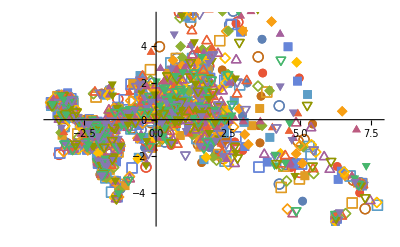

```mathematica
ListPlot[List/@xy,PlotMarkers->Automatic]
```

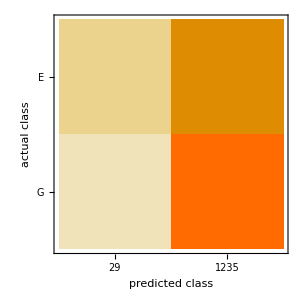

```mathematica
cm["ConfusionMatrixPlot"]
```

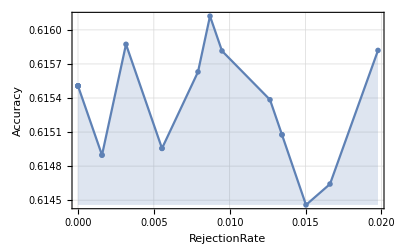

```mathematica
cm["AccuracyRejectionPlot"]
```

```mathematica
loss[{c_,gamma_,b_,d_}]:=-ClassifierMeasurements[Classify[data -> "Phase",Method->{"SupportVectorMachine","KernelType"->"Polynomial","SoftMarginParameter"->Exp[c],"GammaScalingParameter"->Exp[gamma],"BiasParameter"->Exp[b],"PolynomialDegree"->d}],testModel,"LogLikelihoodRate"];
```

```mathematica
region=ImplicitRegion[And[-3.≤c≤3.,-3.≤gamma≤3.,-1.≤b≤2.,1≤d≤3,d∈Integers],{c,gamma,b,d}]
```

ImplicitRegion[-3.≤c≤3.&&-3.≤gamma≤3.&&-1.≤b≤2.&&1≤d≤3&&d∈Integers,{c,gamma,b,d}]

```mathematica
bmo=BayesianMinimization[loss,region]
```

BayesianMinimizationObject[…]

```mathematica
bmo["MinimumConfiguration"]
```

{-1.74287,-2.43011,1.58971,1}

```mathematica
bmo["EvaluationHistory"]
```

Dataset[<>]

```mathematica
c2 = Classify[data -> "Phase"  Method->{"SupportVectorMachine","KernelType"->"Polynomial","SoftMarginParameter"->Exp[2.463183419710031],"GammaScalingParameter"->Exp[-0.008322663130298835],"BiasParameter"->Exp[0.5716911807268561],"PolynomialDegree"->1}]
```

Classify::mlbddata: The data is not formatted correctly.

Classify[Dataset[<>]→Phase Method→{SupportVectorMachine,KernelType→Polynomial,SoftMarginParameter→11.7421,GammaScalingParameter→0.991712,BiasParameter→1.77126,PolynomialDegree→1}]

```mathematica
cm2 = ClassifierMeasurements[c2, testModel]
```

ClassifierMeasurementsObject[…]

```mathematica
cm2["Accuracy"]
```

0.735759

```mathematica
func[method_]:=-ClassifierMeasurements[Classify[data->"Phase",Method->method],testModel,"LogLikelihood"];
methods={"NearestNeighbors","NeuralNetwork","SupportVectorMachine"};
```

```mathematica
bo=BayesianMinimization[func,methods]
```

BayesianMinimizationObject[…]

```mathematica
bo["EvaluationHistory"]
```

Dataset[<>]

```mathematica
bo["MinimumValue"]
```

1101.04

```mathematica
ListPlot[data[;;10]]
```

-Graphics-